## Generating Am241 Spectrum for MilliCharged Detector

The data here is taken from Table 1 and Figure 2 of:
http://www.iaea.org/inis/collection/NCLCollectionStore/_Public/29/041/29041560.pdf
This notebook is used to generate the Am241 spectrum. It outputs the distribution to where geant4 is currently configured to read it from.

Setup : 1 scintillator along y axis (5cm), 1 along z (5cm), x is front (depth, 85cm)
There are 3 locations we should consider for the source:
1: near the scint(about 5cm from end)
2: middle of scint
3: end of scint (about 5cm from end)

The source is placed “on the top” of the bar, with about 1
mm of Al foil (on the bar) and 2 mm of “cloth/paper (G4_CELLULOSE_CELLOPHANE)” outside.

```mathematica
Quit[]
```

### User Settings

```mathematica
pathData=NotebookDirectory[]<>"SourceCalibrationFiles/";
pathOutput=NotebookDirectory[]<>"../";
```

```mathematica
ExposureLengthSeconds=0.1(*seconds/min*);
SourceRadioactivity=39(*kBq*)*1000(*Bq/kBq*);
NumberEvents=SourceRadioactivity*ExposureLengthSeconds
ScintLength=0.85;
```

3900.

```mathematica
Export[pathData<>"EposureLengthSeconds.dat",ExposureLengthSeconds];
Export[pathData<>"SourceRadioactivity.dat",SourceRadioactivity];
Export[pathData<>"NumberEvents.dat",NumberEvents];
```

### Read In Data

```mathematica
(*Energy (keV)*)
MainPeakEnergies={2.88,4.04,6.94,7.85,11.8,13.9,14.6,16.9,17.7,18.8,20.7,21.3,26.3,33.2,49.5,58.6,59.5};
peakWidth=450/1000. 1/2(*keV*);

LowEnergy=Import[pathData<>"Am241SpectrumLowEnergy.csv"];
MedEnergy=Import[pathData<>"Am241SpectrumMediumEnergy.csv"];
HighEnergy=Import[pathData<>"Am241SpectrumHighEnergy.csv"];
histoResolution=0.05(*keV*);

Am241EnergySpectrum=Flatten[{LowEnergy,MedEnergy,HighEnergy},1];
```

### Definitions

```mathematica
(*Samples the Cs137 spectrum given the weights, smeares the output*)
Clear[GenerateRealAm241Spectrum];
GenerateRealAm241Spectrum[EnergySpectrum_,sigma_,n_]:=Block[{NormalizedWeights,weights,peaks,cdf,SamplePDF,SmearedSamplePDF},

peaks=Transpose[EnergySpectrum]⟦1⟧;
weights=Transpose[EnergySpectrum]⟦2⟧;
NormalizedWeights=weights/Total[weights];
cdf=EmpiricalDistribution[NormalizedWeights->peaks];
SamplePDF=RandomVariate[cdf,n];
SmearedSamplePDF=Table[RandomVariate[NormalDistribution[SamplePDF⟦i⟧,sigma]],{i,1,n}];
Return[SmearedSamplePDF];

]

Clear[SampleSine];
SampleSine[n_]:=Block[{dat,rand},

dat=Table[
rand=Random[];
ArcCos[1-2 rand]
,{i,1,n}];

Return[dat];

]

keVToGeV=(10^3(*eV*))/(1(*keV*))*(1(*GeV*))/(10^9(*eV*));
```

### Preliminary Exploration of the Spectrum

```mathematica
(*We see if our random sampling reproduces the observed spectrum*)
```

```mathematica
(*Sample Am241 spectrum*)
dat=GenerateRealAm241Spectrum[Am241EnergySpectrum,peakWidth,7.3*10^5];
```

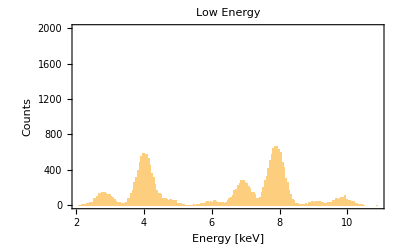

```mathematica
RealSpectrumLowEnergy=Select[dat,#<11&];
Histogram[RealSpectrumLowEnergy,{histoResolution},PlotRange->{0,2000},PlotLabel->"Low Energy",Frame->True,FrameLabel->{"Energy [keV]","Counts"}]
```

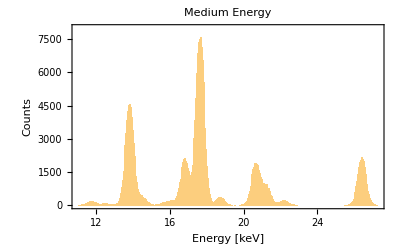

```mathematica
RealSpectrumMediumEnergy=Select[dat,#≥11&&#<30&];
Histogram[RealSpectrumMediumEnergy,{histoResolution},PlotRange->{0,8000},PlotLabel->"Medium Energy",Frame->True,FrameLabel->{"Energy [keV]","Counts"}]
```

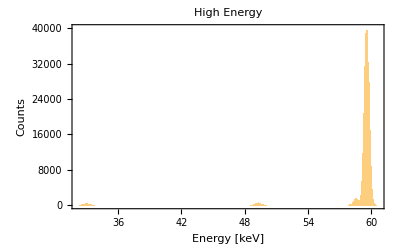

```mathematica
RealSpectrumHighEnergy=Select[dat,#≥30&];
Histogram[RealSpectrumHighEnergy,{histoResolution},PlotRange->{All,{0,4*10^4}},PlotLabel->"High Energy",Frame->True,FrameLabel->{"Energy [keV]","Counts"}]
```

### Spectrum Am241

```mathematica
(*Set How Far from the scintillator the Am241 Source will be*)
xLength={ScintLength-0.05,ScintLength/2,0.05}(*m*);
(*Center the source around the middle of the sinctillator*)
yLength=0.05/2+0.006;
zLength=0;
q=0;m=0;
```

```mathematica
pNorm={Null,Null,Null};
```

```mathematica
(*Format: q m x y z px py pz*)

OutData=Table[

energy(*GeV*)=Round[GenerateRealAm241Spectrum[Am241EnergySpectrum,peakWidth,NumberEvents],0.001]*keVToGeV;
theta=SampleSine[NumberEvents];
phi=Table[2π Random[],{i,1,Length[theta]}];
pNorm⟦j⟧=energy;


Table[{q,m,xLength⟦j⟧,yLength,zLength,pNorm⟦j,i⟧ Cos[theta⟦i⟧],pNorm⟦j,i⟧ Cos[phi⟦i⟧]Sin[theta⟦i⟧],
pNorm⟦j,i⟧ Sin[phi⟦i⟧]Sin[theta⟦i⟧]},{i,1,Length[theta]}]


,{j,1,Length@xLength}
];
Length@OutData⟦1⟧-1
```

3899

```mathematica
Export[pathData<>"MCEnergyDistribution.dat",pNorm]
```

/Users/chaffy/Work/Repository_MilliCharged/milliQan/SourceFiles/GenerateDistributions/SourceCalibrationFiles/MCEnergyDistribution.dat

```mathematica
Export[pathOutput<>"Am241DistributionCloseEnd.dat",OutData⟦1⟧];
Export[pathOutput<>"Am241DistributionMiddle.dat",OutData⟦2⟧];
Export[pathOutput<>"Am241DistributionFarEnd.dat",OutData⟦3⟧];
```

### Spectrum Am241 only 10 and 60keV StraightLine from Top Center

```mathematica
xLength⟦2⟧
```

0.425

```mathematica
nevents=10^5;
pvalues=RandomChoice[{10,10(*60*)},nevents];
OutDataSimple=Table[
{q,m,xLength⟦2⟧,yLength,zLength,ppNorm Cos[ttheta],ppNorm Cos[pphi]Sin[ttheta],ppNorm Sin[pphi]Sin[ttheta]}/.{ttheta->π/2,ppNorm->pvalues⟦i⟧*keVToGeV,pphi->π}//N
,{i,1,nevents}];

Length@OutDataSimple-1
```

99999

```mathematica
Export[pathOutput<>"Am241DistributionCenteredFarEnd10and60keV.dat",OutDataSimple];
```

### What did We Generate?

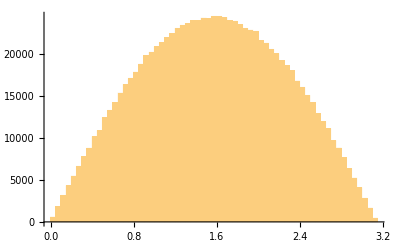

```mathematica
(*We check to make sure the monte carlo above has indeed generated the correct Univerform in Cos distribution*)
Histogram[theta,50]
```

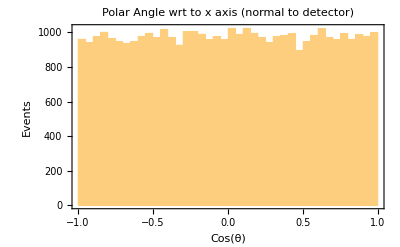

```mathematica
(*We make a histogram of cos(θ)*)
xind=2(*which of the 3 positions on x axis do we want to look at*) ;
Histogram[Table[OutData⟦xind,i,6⟧/pNorm⟦xind,i⟧,{i,1,Length[OutData⟦xind⟧]}],50,PlotLabel->"Polar Angle wrt to x axis (normal to detector)",FrameLabel->{"Cos(θ)","Events"},Frame->True]
```

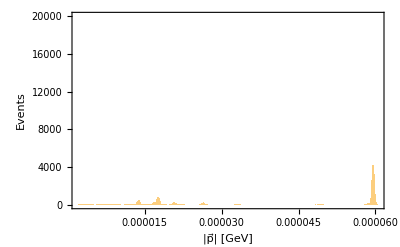

```mathematica
Histogram[pNorm[[3]],400,FrameLabel->{"|p⃗| [GeV]","Events"},Frame->True,PlotRange->{1,20000}]
```

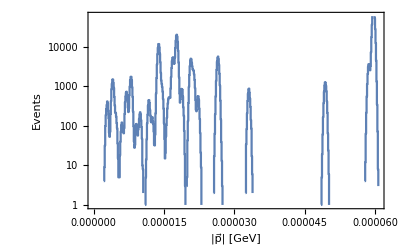

```mathematica
dat=HistogramList[pNorm⟦3⟧,400];
dat=Table[{(dat⟦1,i⟧+dat⟦1,i+1⟧)/2,dat⟦2,i⟧},{i,1,Length@dat⟦2⟧}];
ListLogPlot[dat,PlotLabel->"",FrameLabel->{"|p⃗| [GeV]","Events"},Frame->True,PlotRange->{1,60000},InterpolationOrder->0,Joined->True]
```

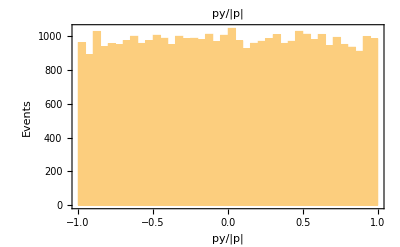

```mathematica
(*We make a histogram of py/|p|*)
xind=1;
Histogram[Table[OutData⟦xind,i,7⟧/pNorm⟦xind,i⟧,{i,1,Length[OutData⟦xind⟧]}],50,PlotLabel->"py/|p|",FrameLabel->{"py/|p|","Events"},Frame->True,PlotRange->All]
```

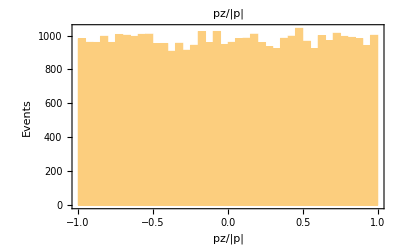

```mathematica
(*We make a histogram of pz/|p|*)
xind=1;
Histogram[Table[OutData⟦xind,i,8⟧/pNorm⟦xind,i⟧,{i,1,Length[OutData⟦xind⟧]}],50,PlotLabel->"pz/|p|",FrameLabel->{"pz/|p|","Events"},Frame->True,PlotRange->All]
```

```mathematica
(*Check to see if we've generated a uniform angular distribution*) 
npoints=5000;
temptheta=SampleSine[npoints];
tempphi=Table[Random[]2π,{i,1,npoints}];

dat=Table[
{Cos[ϕ]*Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]}/.{θ->temptheta⟦i⟧,ϕ->tempphi⟦i⟧}
,{i,1,npoints}];
ListPointPlot3D[dat,BoxRatios->{1,1,1}]
```

-Graphics3D-